## Lab 8 - Gwen Gorman

Find the antiderivative of each function with the help of Mathematica, then, verify the result by finding its derivative. Remember that you might have to apply Simplify.

f(x)=x^3-3x+3

```mathematica
Integrate[x^3-3x+3,x]
```

3 x-(3 x^2)/2+x^4/4

```mathematica
D[(3 x-(3 x^2)/2+x^4/4), x]
```

3-3 x+x^3

f(x)=(x-1)/(x(x+1))

```mathematica
Integrate[(x-1)/(x(x+1)),x]
```

-Log[x]+2 Log[1+x]

```mathematica
D[(-Log[x]+2 Log[1+x]), x]
```

-1/x+2/(1+x)

```mathematica
Simplify[-1/x+2/(1+x)]
```

(-1+x)/(x (1+x))

f(x)=ⅇ^x cos x

```mathematica
Integrate[ⅇ^x Cos[x],x]
```

1/2 ⅇ^x (Cos[x]+Sin[x])

```mathematica
D[(1/2 ⅇ^x (Cos[x]+Sin[x])), x]
```

1/2 ⅇ^x (Cos[x]-Sin[x])+1/2 ⅇ^x (Cos[x]+Sin[x])

```mathematica
Simplify[1/2 ⅇ^x (Cos[x]-Sin[x])+1/2 ⅇ^x (Cos[x]+Sin[x])]
```

ⅇ^x Cos[x]

f(x)=x^2 sin 3x

```mathematica
Integrate[x^2 Sin [3x],x]
```

-1/27 (-2+9 x^2) Cos[3 x]+2/9 x Sin[3 x]

```mathematica
D[(-1/27 (-2+9 x^2) Cos[3 x]+2/9 x Sin[3 x]), x]
```

2/9 Sin[3 x]+1/9 (-2+9 x^2) Sin[3 x]

```mathematica
Simplify[2/9 Sin[3 x]+1/9 (-2+9 x^2) Sin[3 x]]
```

x^2 Sin[3 x]

Without using DSolve or NDSolve, solve each initial-value problem and plot its solution.

y'=2x cos x,y(0)=2

```mathematica
f[x_]:=2x Cos[x]
F[x_]= Integrate[f[x],x]+C
```

C+2 (Cos[x]+x Sin[x])

```mathematica
Solve[F[0]==2,C]//Flatten
```

{C→0}

```mathematica
G[x_]=F[x]/.%
```

2 (Cos[x]+x Sin[x])

```mathematica
G'[x]==f[x]//Simplify
```

True

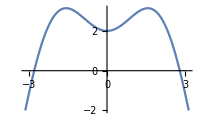

```mathematica
Plot[G[x],{x,-Pi,Pi},ImageSize->200]
```

y''=2x -1,y(1)=0,y'(1)=2

```mathematica
f[x_]:=2x-1
F[x_]= Integrate[f[x],x]+C
```

C-x+x^2

```mathematica
Solve[F[1]==2,C]//Flatten
```

{C→2}

```mathematica
G[x_]=F[x]/.%
```

2-x+x^2

```mathematica
H[x_]=Integrate[G[x],x]+C
```

C+2 x-x^2/2+x^3/3

```mathematica
Solve[H[1]==0,C]//Flatten
```

{C→-11/6}

```mathematica
M[x_]=H[x]/.%
```

-11/6+2 x-x^2/2+x^3/3

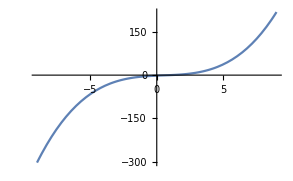

```mathematica
Plot[-11/6+2 x-x^2/2+x^3/3,{x,-9.,9.}]
```

y'+2/x y=x+1,y(1)=1,x>0

```mathematica
Clear["Global`*"]
```

```mathematica
SolveFirstOrderLinearDiffEq[pfunc_,qfunc_] :=Module[{P,Q,μ},
P[X_]=pfunc/.x->X;
Q[X_]=qfunc/.x->X;
μ[x_]=E^Integrate[P[x],x];
1/μ[x] (Integrate[μ[x]Q[x],x]+C)]
```

```mathematica
f[x_]=SolveFirstOrderLinearDiffEq[2/x,x+1]//Simplify
```

C/x^2+1/12 x (4+3 x)

```mathematica
Solve[f[1]==1,C]//Flatten
```

```mathematica
{C->5/12}
G[x_]=f[x]/.%
```

{C→5/12}

5/(12 x^2)+1/12 x (4+3 x)

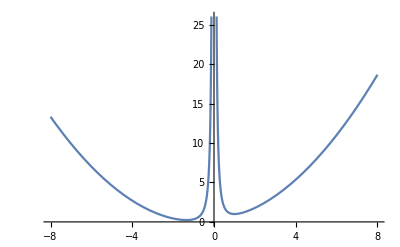

```mathematica
Plot[5/(12 x^2)+1/12 x (4+3 x),{x,-8,8}]
```

Using DSolve, solve the initial-value problem y'=2x cos x,y(0)=2.

```mathematica
f[x_]=(y[x]/.DSolve[y'[x]==2x*Cos[x],y[x],x])[[1]]
```

C[1]+2 (Cos[x]+x Sin[x])

```mathematica
Solve[f[0]==2,C[1]]
```

{{C[1]→0}}

```mathematica
f[x_]=f[x]/.%[[1]]
```

2 (Cos[x]+x Sin[x])

Using DSolve, solve the initial-value problem y''=2x -1,y(1)=0,y'(1)=2.

```mathematica
f[x_]=(y[x]/.DSolve[y''[x]==2x-1,y[x],x])[[1]]
```

-x^2/2+x^3/3+C[1]+x C[2]

```mathematica
Solve[f'[1]==2,C[2]]
```

{{C[2]→2}}

```mathematica
Solve[f[1]==0,C[1]]
```

{{C[1]→1/6 (1-6 C[2])}}

```mathematica
f[x_]=f[x]/.%[[1]]
```

-11/6+2 x-x^2/2+x^3/3

Using DSolve, find a general solution to the differential equation y'=y^2 cos x-2y.

```mathematica
Clear["Global`*"]
```

```mathematica
y[x]/.DSolve[y'[x]==y[x]^2*Cos[x]-2y[x],y[x],x]
```

{5/(5 ⅇ^(2 x) C[1]+2 Cos[x]-Sin[x])}

Using NDSolve, solve y'=y^2 cos x-2y,y(0)=1, for 0<x≤2π, and plot your numerical solution.

```mathematica
Clear["Global`*"]
NDSolve[{y'[x]== y[x]^2*Cos[x]-2y[x],y[0]==1},y,{x,0,2Pi}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
f=y/.%[[1]]
```

InterpolatingFunction[…]

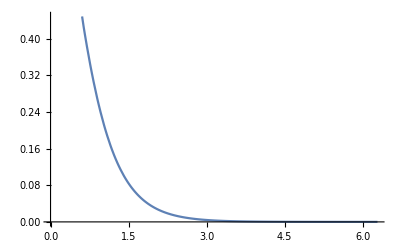

```mathematica
Plot[f[x],{x,0.,6.283185307179586}]
```

Given the following data set, use Interpolation to find an interpolation of the data set, plot the interpolating function, and estimate the value of y at x=1.5 and 4.34, respectively.

```mathematica
points={{1,5},{2,5},{3,1},{4,1},{5,3},{6,4},{7,6},{8,5},{9,0},{10,2}}
f=Interpolation[points]
```

{{1,5},{2,5},{3,1},{4,1},{5,3},{6,4},{7,6},{8,5},{9,0},{10,2}}

InterpolatingFunction[…]

```mathematica
f[1.5]
```

6.

```mathematica
f[4.34]
```

1.60595

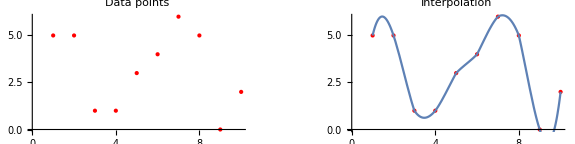

```mathematica
GraphicsRow[{
ListPlot[points,ImageSize->200,PlotStyle->{Red,PointSize[Medium]},PlotLabel->"Data points"],
Show[{
ListPlot[points,ImageSize->200,PlotStyle->{Red,PointSize[Medium]},PlotLabel->"Interpolation"],
Plot[f[x],{x,1,10}]
}]
},Spacings->50]
```

Plot the slope field of the equation y'=sin x cos y together with five particular solutions for -3≤x≤3 and -3≤y≤3.

```mathematica
DirectionFieldWithSolutionCurves[func_,{x_,xMin_,xMax_},{y_,yMin_,yMax_},numOfSoluCurves_:5]:=Module[{f,Y},
f[X_,Y_]=func/.{x->X,y->Y};
Y[c_]=y[x]/.DSolve[y'[x]==f[x,y[x]],y[x],x][[1]]/.C[1]->c;
Show[{
VectorPlot[{1,f[x,y]},{x,xMin,xMax},{y,yMin,yMax},VectorPoints->12,ImageSize->300],
Plot[Evaluate[Table[Y[c],{c,numOfSoluCurves}]],{x,xMin,xMax},PlotStyle->Map[Hue,0.85+.15Range[numOfSoluCurves]]]
}]
];
```

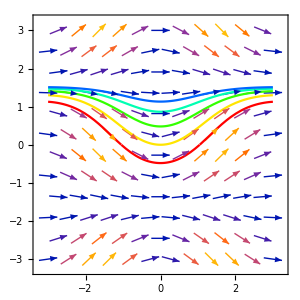

```mathematica
DirectionFieldWithSolutionCurves[Sin[x]Cos[y],{x,-3,3},{y,-3,3},5]
```

Use the function DirectionFieldPlot to play with y'=sin x for -2π≤x≤2π and -3≤y≤3. What analytical solution does the slope field suggest in general?

```mathematica
Clear["Global`*"]
```

```mathematica
DirectionFieldPlot[func_,{x_,xMin_,xMax_},{y_,yMin_,yMax_}]:=
Manipulate[
DynamicModule[{f,Y,c,curves={},xy,new,i,count},
f[X_,Y_]=func/.{x->X,y->Y}; (* y' = f(x,y) *)
Y=y[x]/.DSolve[y'[x]==f[x,y[x]],y[x],x][[1]]/.C[1]->c;(* exact solution *)
EventHandler[
Dynamic[Show[{
VectorPlot[{1,f[x,y]},{x,xMin,xMax},{y,yMin,yMax},VectorPoints->16,VectorStyle->Arrowheads[0.018],ImageSize->300scale],
(* draw previous solution curves *)
count=Length[curves];
Plot[Table[Y/.c->curves[[i,2]],{i,count-1}],{x,xMin,xMax},PlotStyle->Blue],
Graphics[{Blue,PointSize[Large],Point[Table[curves[[i,1]],{i,count-1}]]}],
(* draw solution curve at newly selected point *)
If[count≥1,{
Graphics[{Red,PointSize[Large],Point[curves[[count,1]]]}],
Plot[Y/.c->curves[[count,2]],{x,xMin,xMax},PlotStyle->{Thick,Red}]
},{}] (* {} is required -:) *)
}]],
"MouseClicked":>(
xy=MousePosition["Graphics"];
(* to add a new curve or to remove a previous curve? *)
new=True; i=1;
While[i ≤ Length[curves], If[Total[ (curves[[i,1]]-xy)^2]<1/(10^2.3 scale),new=False;Break[]];i++];
curves=If[new,
Append[curves,{xy,c/.NSolve[(Y/.x->xy[[1]])==xy[[2]],c][[1]]}],
Delete[curves,i]]
)]
],{{scale,1,"Scale"},1,2.5,0.1}]
```

```mathematica
Clear[x,y]
DirectionFieldPlot[Sin[x],{x,-2Pi,2Pi},{y,-3,3}]
```

the slope field is a graphical representation of a differential equation. Analytically, the graph is an image of the solution curves. The slope is determined by evaluating the derivative at the midpoint of the segment.

Using the function AnimateEulerMethod, play with y'=sin x, y(0)=1 on the interval [0,2π]. Note: The exact solution is y=2-cos x.

```mathematica
AnimateEulerMethod[func_,Func_,{x0_,y0_},{a_,b_},plotOptions___]:=
Manipulate[
Module[{f,F,h,points},
f[X_,Y_]=func/.{x->X,y->Y};
F[X_]=Func/.{x->X,y->Y};

h=(b-a)/n;
euler[{x_,y_}]:={x+h,y+f[x,y]*h};
points=NestList[euler,{x0,y0},n];

Show[{
Plot[F[x],{x,a,b},PlotStyle->{Blue,Thickness[0.01]},plotOptions,ImageSize->330],
ListPlot[points,PlotStyle->{Red,PointSize[Medium]}],
Graphics[{Red,Line[points]}]
}]
],{{n,20},1,200,1,Appearance->"Open"}]
Clear[x]
AnimateEulerMethod[Sin[x],2-Cos[x],{0,1},{0,2Pi},PlotRange->{0,2Pi}]
```

Use Euler’s method to find and plot the approximate solution to y'=1+x sin x, y(1)=2 for 1≤x≤2π with n=20.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=1+x* Sin[x];
a=1;b=2Pi;n=20;
h=(b-a)/n;
euler[{x_,y_}]:={x+h,y+f[x,y]*h};
points=NestList[euler,{1,2},n];
```

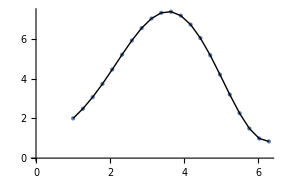

```mathematica
Show[{
ListPlot[points,PlotStyle->PointSize[Medium],ImageSize->200],
Graphics[Line[points]]
}]
```